```mathematica
SetDirectory[NotebookDirectory[]<>"/../"];
<<SimulationRewardDriven1`;
SetDirectory[NotebookDirectory[]];
(*displays results of simulation*)
PlotBelief1[]:=Table[Mean/@BELIEF[[i]],{i,1,BELIEF//Length}]//ListLinePlot[#,AxesLabel->{Style["j",Large],Style["d",Large]},PlotRange->All,PlotLegends->Table[Style["a= "<>ToString[AffinityValues[[i]]]<>", b="<>ToString[BiasValues[[i]]],Large],{i,1,AffinityValues//Length}],ImageSize->Large,TicksStyle->Directive["Label", 20]]&;
```

```mathematica
nquestionsUSER=1000;
nexperimentsUSER=10;
npredictorsUSER=10;
d=ConstantArray[2,npredictorsUSER];
a=ConstantArray[500,npredictorsUSER];
b=ConstantArray[0,npredictorsUSER];
h=ConstantArray[0.99,npredictorsUSER];
InitSimulationRewardDriven[d,a,b,h]
```

Run simulation. 
This runs a ‘for-loop’, each iteration corresponds to an experiment. The first iteration uses values set up above for d,a,b,h. 
The degree of belief d is updated according to a,b,h. At the end of every iteration, the values of a,b are changed to be used for the next iteration.
The value of h stays constant during the entire simulation.

```mathematica
For[it=1,it≤nexperimentsUSER,it++,
(*stores values of a,b for all iterations*)
AppendTo[AffinityValues,a//Mean];
AppendTo[BiasValues,b//Mean];
(*to show progress*)
templine=PrintTemporary[Style["it=",Large,Bold],Style[it,Large,Bold]];
(*initialize experiment*)
InitExperimentRewardDriven[d,a,b,h];
(*run experiment*)
RunExperiment[];
(*saves data on degree of belief during the simulation*)
StoreBeliefCurrent[];
(*change values of a,b for next iteration*)
(*deletes display of progress *)
NotebookDelete[templine]];
```

General::munfl: Exp[-1220.82] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-909.273] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-893.616] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Plot results
use function ‘PlotBelief1[]’ to see results. Relevant data is stored in the various “superarrays” of ‘EQLab’ and a new one called ‘BELIEF’. After running the initialization step, everything gets wiped out, so please save and organize your progress before running a new simulation.

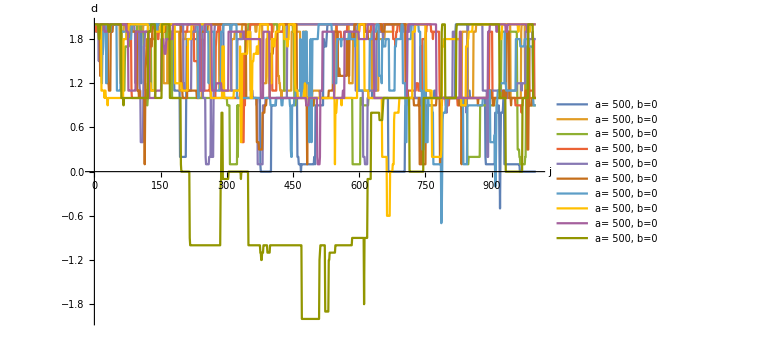

```mathematica
plot1=PlotBelief1[]
```